```mathematica
Clear["Global`*"]
```

```mathematica
scaling=1;
a=scaling N[14/10];   (* == Carbon-Carbon Distance in A == *)
a0=√3 a ;(* == Lattice Constant Graphene == *) (*WARNING a0!=2.46, a0=2.42487*)

(* == Direct Lattice == *)
a1=a0{1,0};  a2=a0{1/2,(√3)/2};                           (* == Direct Lattice Vectors == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);                             (* == High symmetry points == *)
kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);

(* == Reciprocal Lattice == *)

{b1,b2}=2 π Inverse[Transpose[{a1,a2}]];  (* == Reciprocal Lattice Vectors == *)

b3=-( b1+b2);  
kg={0,0}; kp=1/3*(2 b1+b2);                             (* == High symmetry points == *)
km=1/2(b1+b2);  kk=1/3(b1+2 b2);


n=3600;(*Nk=3 n^2*) (* n = number of points that the mesh of the full 1BZ (with same Δk distance) would have*)
δn=120; (* δn = parameter analogous to n, but for the mini-kmesh*)
λ=(n-δn); (* λ is used when generating the meshes*)
Nq=n/2; (*Nq = is the number of q points for which Π(q) will be calculated*)
{iqf,jqf}={0,n/2}; (*The indices of the vector pointing to the end of the q-path*)
(*In order to move in other direction, it might be convenient to project j along other kp vector*)

Npockets=2;
Vpocket=Table[0.,{i,1,Npockets}];
(*Defining where each pocket is centered at:*)
Vpocket[[1]]=kg;

Vpocket[[2]]=kp;
(*
Vpocket[[3]]=kp;
Vpocket[[4]]=0;
*)
(*This function transltes from indices i,j to vectors: *)
(*In this function, the j is projected onto the direction of the q-path*)
IndexToVector[kij_,k0_]:=Module[{sol},
sol=Table[kij[[i,j]].(1/n{kp,kp-kk})+k0,{i,1,Length[kij]},{j,1,Length[kij[[i]]]}]
];

k0ij=Module[{sol},
sol=Table[{i,j},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]}]
];
k0pmesh=Table[IndexToVector[k0ij,Vpocket[[i]]],{i,1,Npockets}];

kqpathpij=Module[{sol},
sol=Table[{i,j},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]+jqf}]
];
kqpathpmesh=Table[IndexToVector[kqpathpij,Vpocket[[i]]-km],{i,1,Npockets}];
iq=Nq/4;
(*
kqij=Apply[{#1,#2-Nq+iq} &,k0ij,{2}];
*)

iq=0.Nq;
kqij=Apply[kqpathpij[[#1+(n-λ),#2+iq-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}];

kqpmesh=Table[IndexToVector[kqij,Vpocket[[i]]-km],{i,1,Npockets}];
```

2.42487

1.72743

1.72743

1.72743

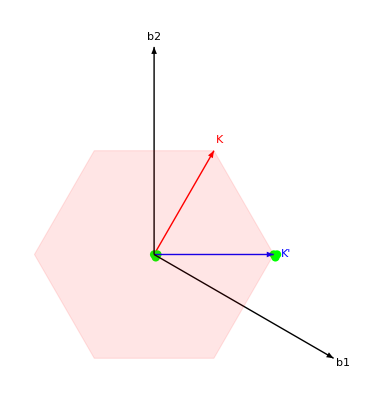

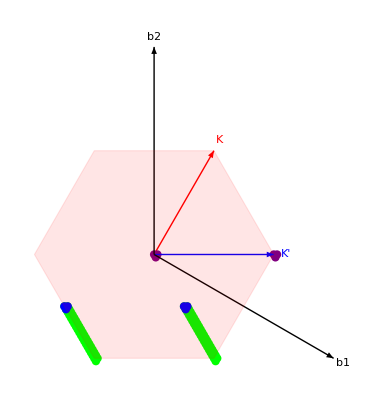

```mathematica
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a0))*{-1,0},((4π)/(3a0))*{(-1)/2,(√3)/2},((4π)/(3a0))*{1/2,(√3)/2},((4π)/(3a0))*{1,0},((4π)/(3a0))*{1/2,(-√3)/2},((4π)/(3a0))*{(-1)/2,(-√3)/2}}];
ps=0.015;
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.1],EdgeForm [Dashed],
BZcontour
}];
a0
Norm[kk]
Norm[kp]
N[4 π/(3 a0)]
(*Plotting the k mesh: *)

Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[k0pmesh[[i]],1]],{i,1,Npockets}]}],
BZvectors
]

ip=1;
ii=0;

Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[kqpathpmesh[[i]],1]],{i,1,Npockets}],
Blue,
Table[Point[Flatten[kqpmesh[[i]],1]],{i,1,Npockets}],
Purple,
Table[Point[Flatten[k0pmesh[[i]],1]],{i,1,Npockets}]
(*
,
Red,
Point[Table[kqpathpmesh[[ip]][[ii+(n-λ),i-Max[-(n-λ),-(n-λ)-ii]]],{i,iq-δn+1+ 0.(-(n-λ)),iq+(n-λ)}]]
*)
}],
BZvectors
]
```

```mathematica
(*a=2.46;a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a0]*Exp[-ⅈ*ky*a0*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a0*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.052175;(* VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
δc=10.*kbT; (*cutoff for the Fermi-Dirac distribution*)
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
(*These arrays hold the same {i,j} structure than kij*)
Ekqpathpij=Table[Map[Eigenvalues,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
ψkqpathpij=Table[Map[Eigenvectors,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
nfEkqpathpij=Table[Map[FDif[#]&,Ekqpathpij[[i]],{3}],{i,1,Npockets}];

Ekqpathpij0=Table[Map[Eigenvalues,Apply[Hk,k0pmesh[[i]],{2}],{2}],{i,1,Npockets}];
ψkqpathpij0=Table[Map[Eigenvectors,Apply[Hk,k0pmesh[[i]],{2}],{2}],{i,1,Npockets}];
nfEkqpathpij0=Table[Map[FDif[#]&,Ekqpathpij0[[i]],{3}],{i,1,Npockets}];


Ek=Flatten[Table[Flatten[Apply[Ekqpathpij0[[i]][[#1+(n-λ),#2+0.n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
ψk=Flatten[Table[Flatten[Apply[ψkqpathpij0[[i]][[#1+(n-λ),#2+0.n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
nfEk=Flatten[Table[Flatten[Apply[nfEkqpathpij0[[i]][[#1+(n-λ),#2+0.n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
```

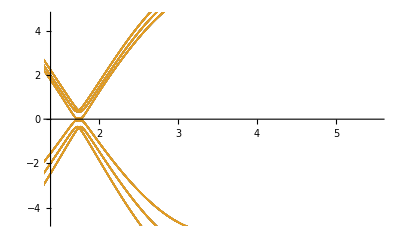

```mathematica
i=0;
ip=1;
iq=Nq;


Epath=Table[
Flatten[Table[{(ii+iq+δn) Norm[kk/n],Ekqpathpij[[ip]][[i+(n-λ),ii+iq-Max[-(n-λ),-(n-λ)-i]]][[j]]},{ii,-(n-λ)+1-Nq, (n-λ)},{j,Nb}],1]
,{ip,1,Npockets}];

(*
Epath=Table[
Flatten[Table[{(ii+δn) Norm[kk/n],Ekqpathpij[[ip]][[i+(n-λ),ii-Max[-(n-λ),-(n-λ)-i]]][[j]]},{ii,iq-δn+1, (n-λ)+iq},{j,Nb}],1]
,{ip,1,Npockets}];
*)
K0=Norm[kk/n] Nq + 0. Vpocket[[1]][[1]] +0. Norm[Vpocket[[ip]]];
δK=1.2Norm[kk];
δE=1.5 γ0;
ListPlot[Epath,PlotRange->{{K0-δK,K0+δK},{-δE,δE}}]
```

```mathematica
qstep=Nq/10(*size of q-steps in units of Δk spacings*)
Lq=2 Norm[kk];
(*Nq=2n;*)(*5200*)
Δq=Lq/Nq;
ω=0.;
(*
Δqij={0.,qstep};
Δq=Norm[Δqij.{kp/n,kk/n}];
Lq=Δq*Nq/qstep;
qi=Table[{(i qstep - Nq/2.) Δq,0.},{i,0,Nq/qstep}];
(*ERROR: why successive qi's are separated by Δq? shouldnt be Δq*qstep? *)
*)
```

180

{{0,0.0014475},{180,0.00155317},{360,0.00168767},{540,0.00186379},{720,0.00210245},{900,0.00244014},{1080,0.00294651},{1260,0.00377348},{1440,0.00532871},{1620,0.00897215},{1800,0.0925861}}

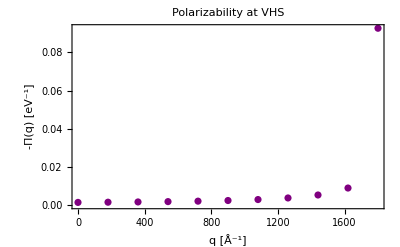

```mathematica
Πq0=Table[{0.,0.},{i,1,Nq/qstep+1}];
Monitor[

For[i=0,i≤Nq/qstep,i++,

q=i Δq;  (*Used for progress bar only*)

Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];

ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;

ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];


Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];


idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq0[[i+1,1]]=i qstep;
Πq0[[i+1,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0,1.1Δq Nq/qstep}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
Πq0
Show[ListPlot[Πq0, PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

{{0,0.0014475},{180,0.00155317},{360,0.00168767},{450,0.00176947},{540,0.00186379},{630,0.00197352},{720,0.00210245},{810,0.00225567},{900,0.00244014},{990,0.00266567},{1080,0.00294651},{1125,0.00311402},{1170,0.00330429},{1215,0.00352206},{1260,0.00377348},{1305,0.00406667},{1350,0.00441257},{1395,0.00482622},{1440,0.00532871},{1462,0.0056153},{1485,0.00594989},{1507,0.00630875},{1530,0.00673077},{1552,0.00718514},{1575,0.00771776},{1597,0.00828319},{1620,0.00897215},{1631,0.00945576},{1642,0.0101997},{1653,0.0116727},{1665,0.0160131},{1676,0.0182474},{1687,0.02144},{1698,0.0263748},{1710,0.0375054},{1721,0.0458694},{1732,0.0481946},{1743,0.0511072},{1755,0.0567137},{1766,0.0691119},{1777,0.104138},{1788,0.11277},{1800,0.0925861}}

{1692,1703,1715,1748,1760,1771,1782,1793}

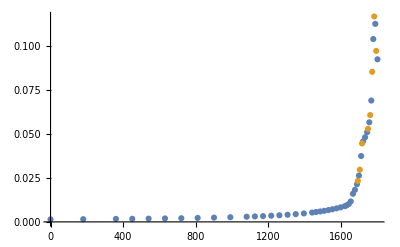

{{0,0.0014475},{180,0.00155317},{360,0.00168767},{450,0.00176947},{540,0.00186379},{630,0.00197352},{720,0.00210245},{810,0.00225567},{900,0.00244014},{990,0.00266567},{1080,0.00294651},{1125,0.00311402},{1170,0.00330429},{1215,0.00352206},{1260,0.00377348},{1305,0.00406667},{1350,0.00441257},{1395,0.00482622},{1440,0.00532871},{1462,0.0056153},{1485,0.00594989},{1507,0.00630875},{1530,0.00673077},{1552,0.00718514},{1575,0.00771776},{1597,0.00828319},{1620,0.00897215},{1631,0.00945576},{1642,0.0101997},{1653,0.0116727},{1665,0.0160131},{1676,0.0182474},{1687,0.02144},{1698,0.0263748},{1710,0.0375054},{1721,0.0458694},{1732,0.0481946},{1743,0.0511072},{1755,0.0567137},{1766,0.0691119},{1777,0.104138},{1788,0.11277},{1800,0.0925861}}

{{1692,0.0233145},{1703,0.0297013},{1715,0.0446699},{1748,0.0529752},{1760,0.0608205},{1771,0.0854721},{1782,0.116983},{1793,0.0973583}}

{{0,0.0014475},{180,0.00155317},{360,0.00168767},{450,0.00176947},{540,0.00186379},{630,0.00197352},{720,0.00210245},{810,0.00225567},{900,0.00244014},{990,0.00266567},{1080,0.00294651},{1125,0.00311402},{1170,0.00330429},{1215,0.00352206},{1260,0.00377348},{1305,0.00406667},{1350,0.00441257},{1395,0.00482622},{1440,0.00532871},{1462,0.0056153},{1485,0.00594989},{1507,0.00630875},{1530,0.00673077},{1552,0.00718514},{1575,0.00771776},{1597,0.00828319},{1620,0.00897215},{1631,0.00945576},{1642,0.0101997},{1653,0.0116727},{1665,0.0160131},{1676,0.0182474},{1687,0.02144},{1692,0.0233145},{1698,0.0263748},{1703,0.0297013},{1710,0.0375054},{1715,0.0446699},{1721,0.0458694},{1732,0.0481946},{1743,0.0511072},{1748,0.0529752},{1755,0.0567137},{1760,0.0608205},{1766,0.0691119},{1771,0.0854721},{1777,0.104138},{1782,0.116983},{1788,0.11277},{1793,0.0973583},{1800,0.0925861}}

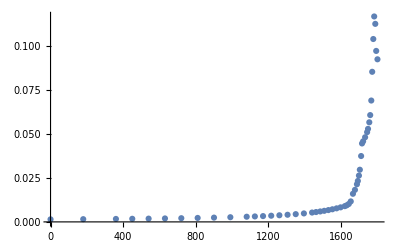

{-1.72743,-1.38194,-1.03646,-0.863714,-0.690971,-0.518228,-0.345486,-0.172743,0.,0.172743,0.345486,0.431857,0.518228,0.6046,0.690971,0.777343,0.863714,0.950085,1.03646,1.07868,1.12283,1.16505,1.2092,1.25143,1.29557,1.3378,1.38194,1.40306,1.42417,1.44528,1.46831,1.48943,1.51054,1.52014,1.53165,1.54125,1.55469,1.56428,1.5758,1.59691,1.61802,1.62762,1.64106,1.65065,1.66217,1.67177,1.68328,1.69288,1.7044,1.71399,1.72743}

{{-1.72743,0.0014475},{-1.38194,0.00155317},{-1.03646,0.00168767},{-0.863714,0.00176947},{-0.690971,0.00186379},{-0.518228,0.00197352},{-0.345486,0.00210245},{-0.172743,0.00225567},{0.,0.00244014},{0.172743,0.00266567},{0.345486,0.00294651},{0.431857,0.00311402},{0.518228,0.00330429},{0.6046,0.00352206},{0.690971,0.00377348},{0.777343,0.00406667},{0.863714,0.00441257},{0.950085,0.00482622},{1.03646,0.00532871},{1.07868,0.0056153},{1.12283,0.00594989},{1.16505,0.00630875},{1.2092,0.00673077},{1.25143,0.00718514},{1.29557,0.00771776},{1.3378,0.00828319},{1.38194,0.00897215},{1.40306,0.00945576},{1.42417,0.0101997},{1.44528,0.0116727},{1.46831,0.0160131},{1.48943,0.0182474},{1.51054,0.02144},{1.52014,0.0233145},{1.53165,0.0263748},{1.54125,0.0297013},{1.55469,0.0375054},{1.56428,0.0446699},{1.5758,0.0458694},{1.59691,0.0481946},{1.61802,0.0511072},{1.62762,0.0529752},{1.64106,0.0567137},{1.65065,0.0608205},{1.66217,0.0691119},{1.67177,0.0854721},{1.68328,0.104138},{1.69288,0.116983},{1.7044,0.11277},{1.71399,0.0973583},{1.72743,0.0925861}}

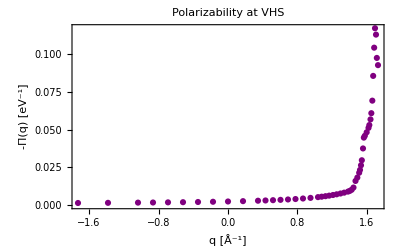

{-1.72743,-1.64106,-1.55469,-1.38194,-1.03646,-0.690971,-0.345486,-0.172743,-0.0863714,0.,0.0863714,0.172743,0.345486,0.690971,1.03646,1.38194,1.55469,1.64106,1.72743}

{{-1.72743,0.0916418},{-1.64106,0.00741892},{-1.55469,0.00479754},{-1.38194,0.00313709},{-1.03646,0.00244659},{-0.690971,0.00277149},{-0.345486,0.00460526},{-0.172743,0.00800003},{-0.0863714,0.0130142},{0.,0.267523},{0.0863714,0.0128703},{0.172743,0.00790812},{0.345486,0.00456061},{0.690971,0.00275821},{1.03646,0.00244667},{1.38194,0.00314624},{1.55469,0.00481847},{1.64106,0.00745834},{1.72743,0.0916477}}

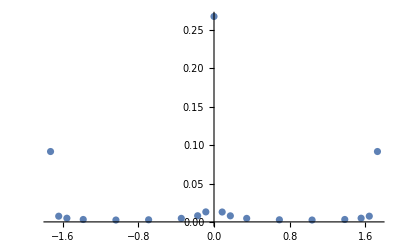

```mathematica
Πq0=DeleteDuplicates[Πq0]

DΠ=Table[{Πq0[[i,1]],(Abs[Πq0[[i+1,2]]-Πq0[[i,2]]]+0.0001)^-1},{i,1,Length[Πq0]-1}];
NiMax=8;(*Must be smaller than initial number of points!*)
qstep=1/2 qstep; (*1 +0.Ceiling[1/2 qstep];*) (*Eventually reaches 1*)

iDmaxOrigi=Floor[Sort[DΠ[[Ordering[DΠ[[All,2]]],1]][[1;;NiMax]]]+qstep]
(*
iDmaxOrigi=Floor[DΠ[[Ordering[DΠ[[All,2]]],1]][[NiMax;;]]+qstep]
*)

Πq02=Table[{0.,0.},{i,1,NiMax}];

Monitor[

For[i=1,i≤NiMax,i++,

q=i Δq;  (*Used for progress bar only*)

Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]] -Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]]-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]]-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];

ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;

ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];


Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];


idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq02[[i,1]]=iDmaxOrigi[[i]];
Πq02[[i,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{Δq,(NiMax+1) Δq}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
Πq02;
(*
Show[ListPlot[Πq02, PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
*)
Show[ListPlot[{Πq0,Πq02},PlotRange->{{0,Nq},All}]]
(*Show[ListPlot[{Πq02},PlotRange->{{0,5200},All}]]*)
Π1p2=Join[Πq0,Πq02];
Ordering[Π1p2[[All,1]]];
Πq0
Πq02
Πq0=Π1p2[[Ordering[Π1p2[[All,1]]]]]
ListPlot[Πq0,PlotRange->All]
qi=Table[ Πq0[[i,1]]  Δq-Norm[kk],{i,1,Length[Πq0]}]
Πq0q=Table[{qi[[i]],Πq0[[i,2]]},{i,1,Length[Πq0]}]
Show[ListPlot[Πq0q, PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True,Axes->False, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

```mathematica
ϵ=40; (*In Fig.1: between 10-20*)
d=400;(*In A.In Fig.1: between 50-400 A*)
e2Coulomb=14.4;(*eV A*)
Vc[qa0_]:=2π e2Coulomb/ϵ a0/Abs[qa0] Tanh[Abs[qa0] d/a0]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

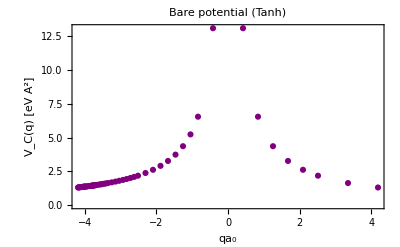

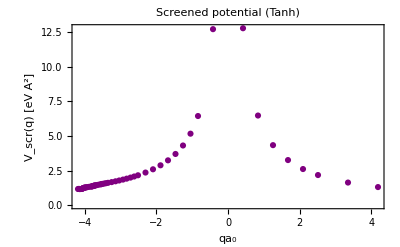

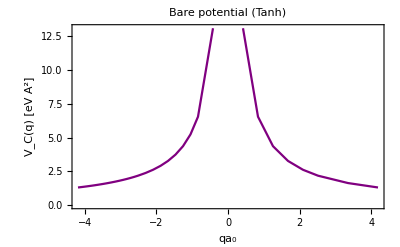

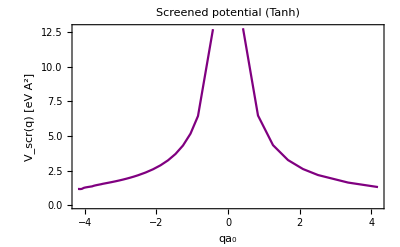

{{0,0.0916418},{8,0.099069},{8,0.099069},{8,0.099069},{12,0.0814874},{14,0.0746495},{15,0.0712246},{15,0.0712246},{15,0.0712246},{32,0.0418061},{65,0.0360103},{67,0.0349372},{68,0.034902},{68,0.034902},{68,0.034902},{130,0.00741892},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2486,0.0142051},{2490,0.0145985},{2492,0.0148274},{2493,0.0149524},{2493,0.0149524},{2493,0.0149524},{2535,0.0632625},{2535,0.0632625},{2535,0.0632625},{2539,0.0818219},{2539,0.0818219},{2539,0.0818219},{2567,0.106169},{2571,0.121465},{2571,0.121465},{2571,0.121465},{2575,0.143678},{2577,0.158638},{2577,0.158638},{2577,0.158638},{2579,0.179131},{2580,0.193017},{2580,0.193017},{2580,0.193017},{2581,0.213015},{2582,0.22966},{2583,0.241878},{2583,0.241878},{2583,0.241878},{2600,0.267523},{2616,0.255454},{2617,0.241869},{2618,0.229648},{2619,0.213002},{2619,0.213002},{2620,0.193001},{2620,0.193001},{2622,0.168131},{2622,0.168131},{2624,0.150583},{2624,0.150583},{2628,0.126237},{2632,0.109193},{2636,0.0973587},{2638,0.0927566},{2639,0.090761},{2639,0.090761},{2665,0.063072},{2665,0.063072},{2673,0.0455644},{2677,0.0397037},{2679,0.0367255},{2679,0.0367255},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5074,0.00758571},{5076,0.00765065},{5077,0.00768347},{5077,0.00768347},{5135,0.0360692},{5167,0.040989},{5167,0.040989},{5183,0.0658735},{5184,0.0682849},{5184,0.0682849},{5200,0.0916477}}

{{0,0.0916418},{8,0.099069},{12,0.0814874},{14,0.0746495},{15,0.0712246},{32,0.0418061},{65,0.0360103},{67,0.0349372},{68,0.034902},{130,0.00741892},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2486,0.0142051},{2490,0.0145985},{2492,0.0148274},{2493,0.0149524},{2535,0.0632625},{2539,0.0818219},{2567,0.106169},{2571,0.121465},{2575,0.143678},{2577,0.158638},{2579,0.179131},{2580,0.193017},{2581,0.213015},{2582,0.22966},{2583,0.241878},{2600,0.267523},{2616,0.255454},{2617,0.241869},{2618,0.229648},{2619,0.213002},{2620,0.193001},{2622,0.168131},{2624,0.150583},{2628,0.126237},{2632,0.109193},{2636,0.0973587},{2638,0.0927566},{2639,0.090761},{2665,0.063072},{2673,0.0455644},{2677,0.0397037},{2679,0.0367255},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5074,0.00758571},{5076,0.00765065},{5077,0.00768347},{5135,0.0360692},{5167,0.040989},{5183,0.0658735},{5184,0.0682849},{5200,0.0916477}}

{{0,0.0916418},{8,0.099069},{8,0.099069},{8,0.099069},{12,0.0814874},{14,0.0746495},{15,0.0712246},{15,0.0712246},{15,0.0712246},{32,0.0418061},{65,0.0360103},{67,0.0349372},{68,0.034902},{68,0.034902},{68,0.034902},{130,0.00741892},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2486,0.0142051},{2490,0.0145985},{2492,0.0148274},{2493,0.0149524},{2493,0.0149524},{2493,0.0149524},{2535,0.0632625},{2535,0.0632625},{2535,0.0632625},{2539,0.0818219},{2539,0.0818219},{2539,0.0818219},{2567,0.106169},{2571,0.121465},{2571,0.121465},{2571,0.121465},{2575,0.143678},{2577,0.158638},{2577,0.158638},{2577,0.158638},{2579,0.179131},{2580,0.193017},{2580,0.193017},{2580,0.193017},{2581,0.213015},{2582,0.22966},{2583,0.241878},{2583,0.241878},{2583,0.241878},{2600,0.267523},{2616,0.255454},{2617,0.241869},{2618,0.229648},{2619,0.213002},{2619,0.213002},{2620,0.193001},{2620,0.193001},{2622,0.168131},{2622,0.168131},{2624,0.150583},{2624,0.150583},{2628,0.126237},{2632,0.109193},{2636,0.0973587},{2638,0.0927566},{2639,0.090761},{2639,0.090761},{2665,0.063072},{2665,0.063072},{2673,0.0455644},{2677,0.0397037},{2679,0.0367255},{2679,0.0367255},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5074,0.00758571},{5076,0.00765065},{5077,0.00768347},{5077,0.00768347},{5135,0.0360692},{5167,0.040989},{5167,0.040989},{5183,0.0658735},{5184,0.0682849},{5184,0.0682849},{5200,0.0916477}}

```mathematica
qia0= a0 Πq0q[[All,1]];
Π=Πq0q[[All,2]];
Vcq=Map[Vc,qia0,{1}];
Vscr=Vcq/(1+Vcq Π);
Show[ListPlot[Transpose[{qia0,Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential (Tanh)"]]]
Show[ListPlot[Transpose[{qia0,Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential (Tanh)"]]]
Show[ListPlot[Transpose[{qia0,Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential (Tanh)"]]]
Show[ListPlot[Transpose[{qia0,Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential (Tanh)"]]]
```

```mathematica
Πq0
```

{{0,0.0916418},{8,0.099069},{12,0.0814874},{14,0.0746495},{15,0.0712246},{16,0.0682635},{32,0.0418061},{65,0.0360103},{67,0.0349372},{68,0.034902},{80,0.0139065},{130,0.00741892},{197,0.00575184},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2486,0.0142051},{2490,0.0145985},{2492,0.0148274},{2493,0.0149524},{2494,0.0150858},{2535,0.0632625},{2539,0.0818219},{2558,0.0862574},{2567,0.106169},{2571,0.121465},{2575,0.143678},{2577,0.158638},{2579,0.179131},{2580,0.193017},{2581,0.213015},{2582,0.22966},{2583,0.241878},{2584,0.255462},{2600,0.267523},{2616,0.255454},{2617,0.241869},{2618,0.229648},{2619,0.213002},{2620,0.193001},{2621,0.179113},{2622,0.168131},{2624,0.150583},{2625,0.143647},{2628,0.126237},{2632,0.109193},{2636,0.0973587},{2638,0.0927566},{2639,0.090761},{2640,0.0890155},{2665,0.063072},{2673,0.0455644},{2677,0.0397037},{2679,0.0367255},{2680,0.0353505},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5074,0.00758571},{5075,0.00761806},{5076,0.00765065},{5077,0.00768347},{5078,0.00771654},{5135,0.0360692},{5167,0.040989},{5168,0.041854},{5183,0.0658735},{5184,0.0682849},{5185,0.071245},{5200,0.0916477}}

{{0,0.0916418},{8,0.099069},{12,0.0814874},{14,0.0746495},{15,0.0712246},{32,0.0418061},{65,0.0360103},{67,0.0349372},{68,0.034902},{80,0.0139065},{130,0.00741892},{197,0.00575184},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2486,0.0142051},{2490,0.0145985},{2492,0.0148274},{2493,0.0149524},{2535,0.0632625},{2539,0.0818219},{2558,0.0862574},{2567,0.106169},{2571,0.121465},{2575,0.143678},{2577,0.158638},{2579,0.179131},{2580,0.193017},{2581,0.213015},{2582,0.22966},{2583,0.241878},{2600,0.267523},{2616,0.255454},{2617,0.241869},{2618,0.229648},{2619,0.213002},{2620,0.193001},{2622,0.168131},{2624,0.150583},{2628,0.126237},{2632,0.109193},{2636,0.0973587},{2638,0.0927566},{2639,0.090761},{2665,0.063072},{2673,0.0455644},{2677,0.0397037},{2679,0.0367255},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5074,0.00758571},{5075,0.00761806},{5076,0.00765065},{5077,0.00768347},{5135,0.0360692},{5167,0.040989},{5183,0.0658735},{5184,0.0682849},{5200,0.0916477}}